```mathematica
Exit
```

DeleteDirectory::nodir: Directory /Users/Henrik/github/CycleSamplerLink/LibraryResources/MacOSX-ARM64 not found.

$Failed

```mathematica
(*Delete all compiled dynamic libraries of the CycleSamplerLink package.*)
If[
FileExistsQ[#],DeleteDirectory[#,DeleteContents->True]
]&[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"LibraryResources",$SystemID}]]
```

```mathematica
Get[
FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CycleSamplerLink.m"}]
]
```

0.120183

0.106627

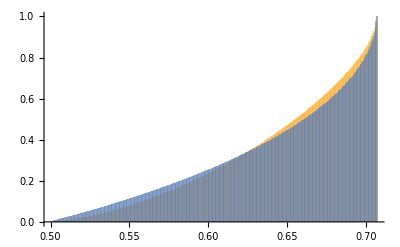

```mathematica
d=3;
r=ConstantArray[1.,4];
samplecount=1000000;
data1=CycleSample["Gyradius",d,r,samplecount,"QuotientSpace"->False];//AbsoluteTiming//First
data2=CycleSample["Gyradius",d,r,samplecount,"QuotientSpace"->True];//AbsoluteTiming//First
Histogram[{data1,data2},"Wand","CDF",PlotRange->All]
```

0.117891

0.105793

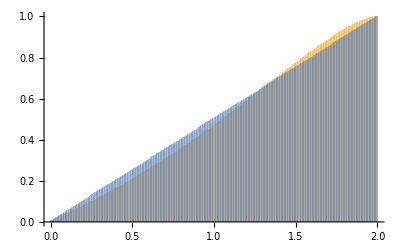

```mathematica
data1=CycleSampleChordLength[d,r,{1,3},samplecount,"QuotientSpace"->False];//AbsoluteTiming//First
data2=CycleSampleChordLength[d,r,{1,3},samplecount,"QuotientSpace"->True];//AbsoluteTiming//First
Histogram[{data1,data2},"Wand","CDF",PlotRange->All]
```

```mathematica
n=40;
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=MomentPolytopeSample[n,1000000];//AbsoluteTiming
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=MomentPolytopeSample[n,1000000];//AbsoluteTiming
```

{0.578515,Null}

{0.526969,Null}

{0.496666,Null}

{0.536138,Null}

```mathematica
n=100;
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=MomentPolytopeSample[n,1000000];//AbsoluteTiming
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=MomentPolytopeSample[n,1000000];//AbsoluteTiming
```

{1.11967,Null}

{2.33521,Null}

{1.13711,Null}

{2.40247,Null}

```mathematica
n=2000;
a=RandomClosedPolygons[3,ConstantArray[1.,n],10000];//AbsoluteTiming
b=MomentPolytopeSample[n,10000];//AbsoluteTiming
a=RandomClosedPolygons[3,ConstantArray[1.,n],10000];//AbsoluteTiming
b=MomentPolytopeSample[n,10000];//AbsoluteTiming
```

{0.277286,Null}

{7.05391,Null}

{0.210957,Null}

{6.85907,Null}